# Homework 6

Name:Eslam Muhammed Ahmed Zenhom

ID: 201700788

## Problem 1 (Section1: 3)

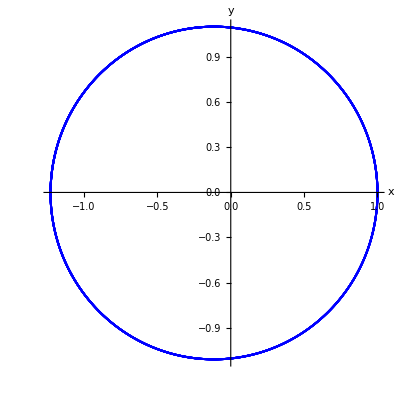

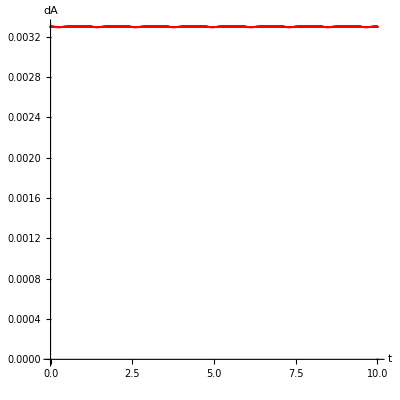

```mathematica
ClearAll["Global`*"]; 
   tmax = 10; 
dt = 0.001; 
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = 1.0; y0 =0.0; 
vx0 = 0.0; vy0 = 2.1Pi;
Tab
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 

dthetaList=0 tL;
dA=0tL;

Do[
rNorm =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
dthetaList[[nt-1]]=VectorAngle[{xList[[nt]],yList[[nt]]},{xList[[nt-1]],yList[[nt-1]]}] ;
dA[[nt-1]]=0.5*rNorm^2*dthetaList[[nt-1]]
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,lt}];
dAtlist=Table[{tL[[j]],dA[[j]]},{j,lt}];
p1 =ListPlot[xylist,PlotStyle->Blue,AspectRatio->1, AxesLabel->{"x","y"}]
p2 =ListPlot[dAtlist,PlotStyle->Red,AspectRatio->1,PlotRange->All,AxesLabel->{"t","dA"}]
(*As you can see in the final plot which is time(where the increments are dt) versus the change in area: it is obvious that the change of area is constant with time which verify kepler second law as this means that the planet sweep same area for same time interval*)
(*I used velocity which 2.1 Pi to make it eeliptical oribit. anyother velocity might be used except 2 pi as this makes the orbit circular*)
```

## Problem 2 (Section1: (5) Circular)

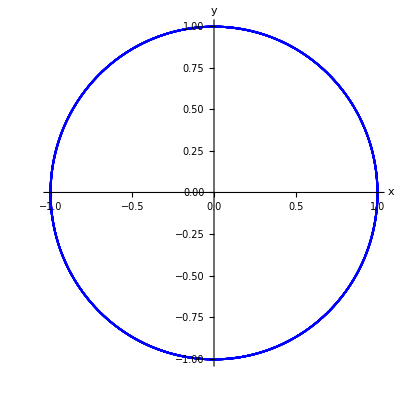

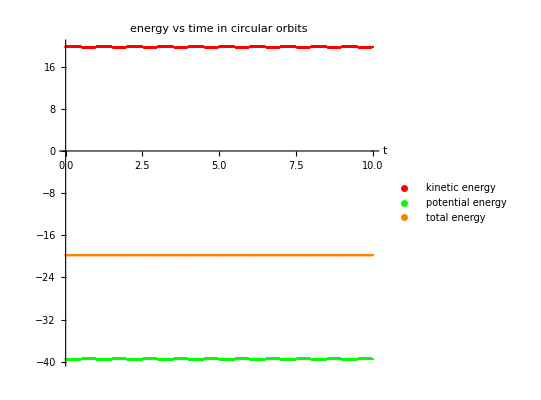

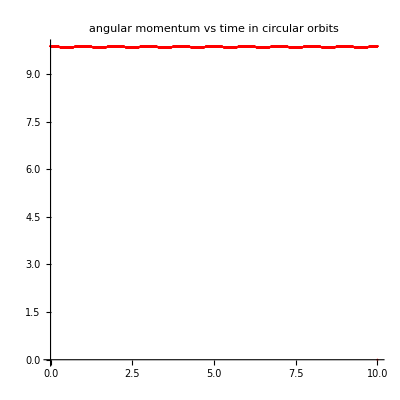

```mathematica
(*Circular*)
ClearAll["Global`*"]; 
   tmax = 10; 
me=1; (*put mass of earth as 1: it wouldn't matter as it will cancel which comparing potential or kientic or total energy*)
dt = 0.001; 
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = 1.0; y0 =0.0; 
vx0 = 0.0; vy0 = 2Pi;
Tab
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 

dthetaList=0 tL;
dA=0tL;
ke=0tL;
pe=0tL;
totale=0tL;
angmomentum=0tL;
Do[
rNorm =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
ke[[nt-1]]=0.5 me (vxList[[nt-1]]^2+vyList[[nt-1]]^2);
pe[[nt-1]]=(-4 Pi^2 me)/rNorm;
totale[[nt-1]]=ke[[nt-1]]+pe[[nt-1]];
angmomentum[[nt-1]]=rNorm me √(vxList[[nt-1]]^2+vyList[[nt-1]]^2)*VectorAngle[{xList[[nt-1]],yList[[nt-1]]},{vxList[[nt-1]],vyList[[nt-1]]}];

dthetaList[[nt-1]]=VectorAngle[{xList[[nt]],yList[[nt]]},{xList[[nt-1]],yList[[nt-1]]}] ;
dA[[nt-1]]=0.5*rNorm^2*dthetaList[[nt-1]]
,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,lt}];
dAtlist=Table[{tL[[j]],dA[[j]]},{j,lt}];
keList=Table[{tL[[j]],ke[[j]]},{j,lt}];
peList=Table[{tL[[j]],pe[[j]]},{j,lt}];
totaleList=Table[{tL[[j]],totale[[j]]},{j,lt}];
angmomentumList=Table[{tL[[j]],angmomentum[[j]]},{j,lt}];
p1 =ListPlot[xylist,PlotStyle->Blue,AspectRatio->1, AxesLabel->{"x","y"}]
p2 =ListPlot[keList,PlotStyle->Red,AspectRatio->1,PlotRange->All,AxesLabel->{"t"},PlotLegends->PointLegend[{"kinetic energy"}]];
p3 =ListPlot[peList,PlotStyle->Green,AspectRatio->1,PlotRange->All,PlotLegends->PointLegend[{"potential energy"}]];
p4 =ListPlot[totaleList,PlotStyle->Orange,AspectRatio->1,PlotRange->All,PlotLegends->PointLegend[{"total energy"}]];
Show[p2,p3,p4,PlotRange->All,PlotLabel-> "energy vs time in circular orbits"]
p5 =ListPlot[angmomentumList,PlotStyle->Red,AspectRatio->1,PlotRange->All,PlotLabel->"angular momentum vs time in circular orbits"]
```

## Problem 3(Section1: (5) Elliptical)

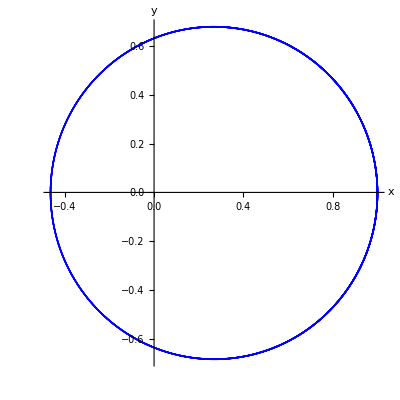

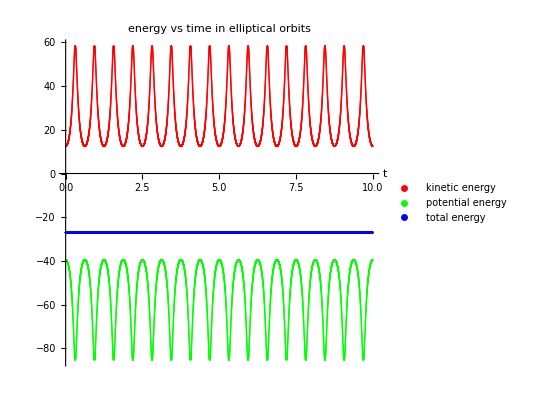

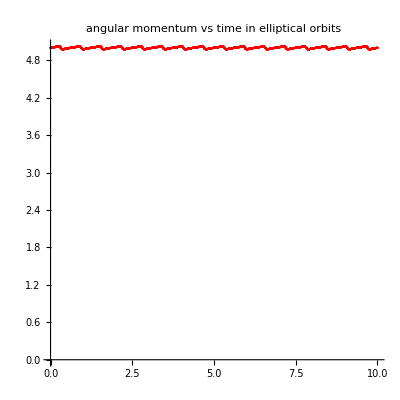

```mathematica
ClearAll["Global`*"]; 
   tmax = 10; 
me=1; (*put mass of earth as 1: it wouldn't matter as it will cancel which comparing potential or kientic or total energy*)
dt = 0.001; 
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = 1.0; y0 =0.0; 
vx0 = 0.0; vy0 = 5;
Tab
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 

dthetaList=0 tL;
dA=0tL;
ke=0tL;
pe=0tL;
totale=0tL;
angmomentum=0tL;
Do[
rNorm =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
ke[[nt]]=0.5 me (vxList[[nt]]^2+vyList[[nt]]^2);
pe[[nt]]=(-4 Pi^2 me)/rNorm;
totale[[nt]]=ke[[nt]]+pe[[nt]];
angmomentum[[nt]]=rNorm* me *√(vxList[[nt]]^2+vyList[[nt]]^2)*Sin[VectorAngle[{xList[[nt]],yList[[nt]]},{vxList[[nt]],vyList[[nt]]}]];


,{nt,2,lt}];
xylist =Table[{xList[[j]],yList[[j]]},{j,lt}];
dAtlist=Table[{tL[[j]],dA[[j]]},{j,lt}];
keList=Table[{tL[[j]],ke[[j]]},{j,lt}];
peList=Table[{tL[[j]],pe[[j]]},{j,lt}];
totaleList=Table[{tL[[j]],totale[[j]]},{j,lt}];
angmomentumList=Table[{tL[[j]],angmomentum[[j]]},{j,lt}];
p1 =ListPlot[xylist,PlotStyle->Blue,AspectRatio->1, AxesLabel->{"x","y"}]
p2 =ListPlot[keList,PlotStyle->Red,AspectRatio->1,PlotRange->All,AxesLabel->{"t"},PlotLegends->PointLegend[{"kinetic energy"}]];
p3 =ListPlot[peList,PlotStyle->Green,AspectRatio->1,PlotRange->All,PlotLegends->PointLegend[{"potential energy"}]];
p4 =ListPlot[totaleList,PlotStyle->Blue,AspectRatio->1,PlotRange->All,PlotLegends->PointLegend[{"total energy"}]];
Show[p2,p3,p4,PlotRange->All,PlotLabel-> "energy vs time in elliptical orbits"]
p5 =ListPlot[angmomentumList,PlotStyle->Red,AspectRatio->1,PlotRange->All,PlotLabel->"angular momentum vs time in elliptical orbits"]
```

## Problem 4 (4.8)

```mathematica
ClearAll["Global`*"]; 
(*earth x0=1,mercury 0.39, venus=0.72, mars=1.52, jupitar 5.2, saturn 9.54 *)
(*earth*) (*all other planets change the a and  e and plug *)
   tmax = 10; 
dt = 0.001; 
a=1; e=0.017;
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = a*(e+1); y0 =0.0; 
vx0 = 0.0; vy0 = √((4 Pi^2*(1-e))/(a (1+e)));
theta=0 tL;
vxList = Table[0,{i,lt}]; vyList = vxList; xList =vxList;yList = vxList; rNorm=0 tL;
rNorm[[1]]=x0;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[rNorm[[nt]] =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm[[nt]]^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm[[nt]]^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
theta[[nt]]=VectorAngle[{x0,0},{xList[[nt]],yList[[nt]]}]
,{nt,2,lt}];
d=FindPeaks[xList][[2]][[1]];
T=tL[[d]];
T^2/a^3

(*mercury*)
ClearAll["Global`*"]; 
(*earth x0=1,mercury 0.39, venus=0.72, mars=1.52, jupitar 5.2, saturn 9.54 *)

   tmax = 10; 
dt = 0.001; 
a=0.39; e=0.206;
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = a*(e+1); y0 =0.0; 
vx0 = 0.0; vy0 = √((4 Pi^2*(1-e))/(a (1+e)));
theta=0 tL;
vxList = Table[0,{i,lt}]; vyList = 0 tL; xList =0 tL;yList = 0 tL; rNorm=0 tL;
rNorm[[1]]=x0;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[rNorm[[nt]] =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm[[nt]]^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm[[nt]]^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
theta[[nt]]=VectorAngle[{x0,0},{xList[[nt]],yList[[nt]]}]
,{nt,2,lt}];

d=FindPeaks[xList][[2]][[1]];
T=tL[[d]];
T^2/a^3
(*mars*)
ClearAll["Global`*"]; 
(*earth x0=1,mercury 0.39, venus=0.72, mars=1.52, jupitar 5.2, saturn 9.54 *)

   tmax = 10; 
dt = 0.001; 
a=0.52; e=0.093;
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = a*(e+1); y0 =0.0; 
vx0 = 0.0; vy0 = √((4 Pi^2*(1-e))/(a (1+e)));
theta=0 tL;
vxList = Table[0,{i,lt}]; vyList = 0 tL; xList =0 tL;yList = 0 tL; rNorm=0 tL;
rNorm[[1]]=x0;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[rNorm[[nt]] =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm[[nt]]^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm[[nt]]^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
theta[[nt]]=VectorAngle[{x0,0},{xList[[nt]],yList[[nt]]}]
,{nt,2,lt}];

d=FindPeaks[xList][[2]][[1]];
T=tL[[d]];
T^2/a^3

(*venus*)
ClearAll["Global`*"]; 
(*earth x0=1,mercury 0.39, venus=0.72, mars=1.52, jupitar 5.2, saturn 9.54 *)

   tmax = 10; 
dt = 0.001; 
a=0.72; e=0.007;
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = a*(e+1); y0 =0.0; 
vx0 = 0.0; vy0 = √((4 Pi^2*(1-e))/(a (1+e)));
theta=0 tL;
vxList = Table[0,{i,lt}]; vyList = 0 tL; xList =0 tL;yList = 0 tL; rNorm=0 tL;
rNorm[[1]]=x0;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[rNorm[[nt]] =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm[[nt]]^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm[[nt]]^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
theta[[nt]]=VectorAngle[{x0,0},{xList[[nt]],yList[[nt]]}]
,{nt,2,lt}];

d=FindPeaks[xList][[2]][[1]];
T=tL[[d]];
T^2/a^3

(*Jupitar*)
ClearAll["Global`*"]; 
(*earth x0=1,mercury 0.39, venus=0.72, mars=1.52, jupitar 5.2, saturn 9.54 *)

   tmax = 100; 
dt = 0.001; 
a=5.2; e=0.048;
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = a*(e+1); y0 =0.0; 
vx0 = 0.0; vy0 = √((4 Pi^2*(1-e))/(a (1+e)));
theta=0 tL;
vxList = Table[0,{i,lt}]; vyList = 0 tL; xList =0 tL;yList = 0 tL; rNorm=0 tL;
rNorm[[1]]=x0;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[rNorm[[nt]] =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm[[nt]]^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm[[nt]]^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
theta[[nt]]=VectorAngle[{x0,0},{xList[[nt]],yList[[nt]]}]
,{nt,2,lt}];

d=FindPeaks[xList][[2]][[1]];
T=tL[[d]];
T^2/a^3

(*saturn*)
ClearAll["Global`*"]; 
(*earth x0=1,mercury 0.39, venus=0.72, mars=1.52, jupitar 5.2, saturn 9.54 *)

   tmax = 100; 
dt = 0.001; 
a=9.54; e=0.054;
tL = Range[0,tmax,dt]; lt = Length[tL];
 x0 = a*(e+1); y0 =0.0; 
vx0 = 0.0; vy0 = √((4 Pi^2*(1-e))/(a (1+e)));
theta=0 tL;
vxList = Table[0,{i,lt}]; vyList = 0 tL; xList =0 tL;yList = 0 tL; rNorm=0 tL;
rNorm[[1]]=x0;
vxList[[1]] = vx0; vyList[[1]] = vy0; 
xList[[1]]   = x0;   yList[[1]]    = y0; 
Do[rNorm[[nt]] =  Sqrt[xList[[nt-1]]^2+yList[[nt-1]]^2];
vxList[[nt]] =vxList[[nt-1]] -4 Pi^2 dt xList[[nt-1]]/rNorm[[nt]]^3;
vyList[[nt]] =vyList[[nt-1]] -4 Pi^2 dt yList[[nt-1]]/rNorm[[nt]]^3;
xList[[nt]]   = xList[[nt-1]] + vxList[[nt]] dt; 
yList[[nt]]   = yList[[nt-1]] + vyList[[nt]] dt;
theta[[nt]]=VectorAngle[{x0,0},{xList[[nt]],yList[[nt]]}]
,{nt,2,lt}];

d=FindPeaks[xList][[2]][[1]];
T=tL[[d]];
T^2/a^3
```

1.

0.995448

1.00012

0.996924

0.999861

0.999994

## Problem5

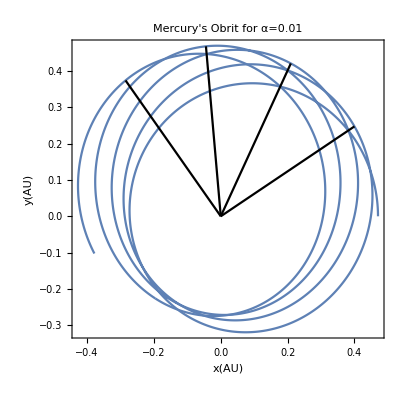

```mathematica
ClearAll["Global`*"]
k=4*π^2;
a=0.39;  e=0.206;
x0=a*(e+1); y0=0;
vx0=0; vy0=√((k*(1-e))/(a (1+e)));
α=0.01;
dt=0.0001; tmax=1; t=Range[0,tmax,dt];
x=0*t; y=0*t;
vx=0*t; vy=0*t;

x[[1]]=x0; y[[1]]=y0;
vx[[1]]=vx0; vy[[1]]=vy0;
apx=List[];  apy=List[]; 
norm=0*t;

 norm[[1]]=√(x[[1]]^2+y[[1]]^2);
For[i=2,i≤Length[t],i++, 
norm[[i]]=√(x[[i-1]]^2+y[[i-1]]^2);
norm3=norm[[i]]^3;

vx[[i]]=vx[[i-1]]-(k x[[i-1]])/norm3*(1+α/norm[[i]]^2) dt;
x[[i]]=x[[i-1]]+vx[[i]] dt;

vy[[i]]=vy[[i-1]]-(k y[[i-1]])/norm3*(1+α/norm[[i]]^2) dt;
y[[i]]=y[[i-1]]+vy[[i]] dt;
];
For[i=1,i≤Length[t],i++,
If[norm[[i]]>norm[[i-1]] && norm[[i]]>norm[[i+1]],
AppendTo[apx,x[[i]]];AppendTo[apy,y[[i]]]]];

apline=0*apx; aplinePlot=0*apx; 
For[i=1,i≤Length[apx],i++,  (*plotting vectors to the aphelions*)
apline[[i]]={apx[[i]],apy[[i]]};
aplinePlot[[i]]=ListLinePlot[{{0,0},{apx[[i]],apy[[i]]}},PlotStyle->Black]
];
xylist=Table[{x[[i]],y[[i]]},{i,Length[t]}];

Quiet[Show[ListLinePlot[xylist,AspectRatio->1,PlotLabel->" Mercury's Obrit for α=0.01",AxesLabel->{"x(AU)","y(AU)"},Frame->True],aplinePlot[[i]]/.i->Range[1,Length[apx]]]]
```

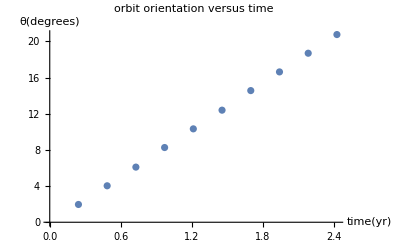

```mathematica
ClearAll["Global`*"]
k=4*π^2;
a=0.39;  e=0.206;
x0=a*(e+1); y0=0;
vx0=0; vy0=√((k*(1-e))/(a (1+e)));
α=0.0008;
dt=0.0001; tmax=2.5; t=Range[0,tmax,dt];
x=0*t; y=0*t;
vx=0*t; vy=0*t;

x[[1]]=x0; y[[1]]=y0;
vx[[1]]=vx0; vy[[1]]=vy0;
apx=List[];  apy=List[];  apt=List[];
norm=0*t;

 norm[[1]]=√(x[[1]]^2+y[[1]]^2);
For[i=2,i≤Length[t],i++, 
norm[[i]]=√(x[[i-1]]^2+y[[i-1]]^2);
norm3=norm[[i]]^3;

vx[[i]]=vx[[i-1]]-(k x[[i-1]])/norm3*(1+α/norm[[i]]^2) dt;
x[[i]]=x[[i-1]]+vx[[i]] dt;

vy[[i]]=vy[[i-1]]-(k y[[i-1]])/norm3*(1+α/norm[[i]]^2) dt;
y[[i]]=y[[i-1]]+vy[[i]] dt;
];
For[i=1,i≤Length[t],i++,
If[norm[[i]]>norm[[i-1]] && norm[[i]]>norm[[i+1]],
AppendTo[apx,x[[i]]];AppendTo[apy,y[[i]]];AppendTo[apt,t[[i]]]]];
θ=0*apx;
For[i=1,i≤Length[apx],i++,  
θ[[i]]=180/π*VectorAngle[{x[[1]],y[[1]]},{apx[[i]],apy[[i]]}]
];
θvstlist=Table[{apt[[i]],θ[[i]]},{i,Length[apx]}];
ListPlot[θvstlist,PlotLabel->" orbit orientation versus time",AxesLabel->{"time(yr)","θ(degrees)"}]
```

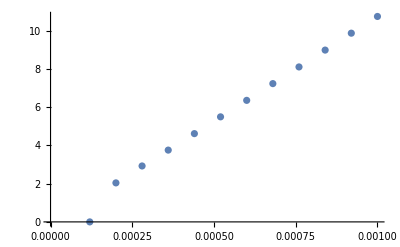

42.0872

```mathematica
ClearAll["Global`*"]
k=4*π^2;
a=0.39;  e=0.206;
x0=a*(e+1); y0=0;
vx0=0; vy0=√((k*(1-e))/(a (1+e)));
α=Range[0.001,0.00008,-0.00008];
dθdt=0*α;
dt=0.0001; tmax=2.5; t=Range[0,tmax,dt];
x=0*t; y=0*t;
vx=0*t; vy=0*t;

For[j=1,j<Length[α],j++,
x[[1]]=x0; y[[1]]=y0;
vx[[1]]=vx0; vy[[1]]=vy0;
apx=List[];  apy=List[];  apt=List[];
norm=0*t;

 norm[[1]]=√(x[[1]]^2+y[[1]]^2);
For[i=2,i≤Length[t],i++, 
norm[[i]]=√(x[[i-1]]^2+y[[i-1]]^2);
norm3=norm[[i]]^3;

vx[[i]]=vx[[i-1]]-(k x[[i-1]])/norm3*(1+α[[j]]/norm[[i]]^2) dt;
x[[i]]=x[[i-1]]+vx[[i]] dt;

vy[[i]]=vy[[i-1]]-(k y[[i-1]])/norm3*(1+α[[j]]/norm[[i]]^2) dt;
y[[i]]=y[[i-1]]+vy[[i]] dt;
];
For[i=1,i≤Length[t],i++,
If[norm[[i]]>norm[[i-1]] && norm[[i]]>norm[[i+1]],
AppendTo[apx,x[[i]]];AppendTo[apy,y[[i]]];AppendTo[apt,t[[i]]]]];
θ=0*apx;
For[i=1,i≤Length[apx],i++,  (*plotting vectors to the aphelions*)
θ[[i]]=180/π*VectorAngle[{x[[1]],y[[1]]},{apx[[i]],apy[[i]]}]
];
θvstlist=Table[{apt[[i]],θ[[i]]},{i,Length[apx]}];
dθdt[[j]]=m/.FindFit[θvstlist,m*time,m,time][[1]]
];
αvsdθdt=Table[{α[[i]],dθdt[[i]]},{i,Length[α]}];
ListPlot[αvsdθdt]
Ω=c/.FindFit[αvsdθdt,c*time,c,time][[1]];
precessionRate=Ω*3600*1.1*10^-8*100
```